# Steiner's tree problem

## In large graphs

## Description

Steiner's tree problem
Input data:
G – undirected graph,
c : E(G) → R^+ – edge weight function,
T ⊆ V(G) – set of terminals
Output data:
steiner's tree for T in G.
i.e. output is G' – tree-subgraph of G : T ⊆ V(G') ∧ c(E(G')) → min.

## Packages

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
AppendTo[$Path, FileNameJoin[{Directory[], "packages"}]];
```

```mathematica
Needs["LeftistHeap`", "data_structures\\leftist_heap.wl"]
```

```mathematica
Needs["Steiner`Utilities`", "steiner_utilities.wl"]
```

```mathematica
Needs["Steiner`Algorithms`GraphUtilities`", "steiner_algorithms_graph_utilities.wl"]
```

```mathematica
Needs["Steiner`Generator`", "steiner_generator.wl"]
Needs["Steiner`SteinLib`", "steiner_steinlib.wl"]
```

```mathematica
Needs["Steiner`Visualization`", "steiner_visualization.wl"]
```

```mathematica
Needs["Steiner`Algorithms`Exact`", "steiner_algorithms_exact.wl"]
```

```mathematica
Needs["Steiner`Algorithms`Dijkstra`", "steiner_algorithms_dijkstra.wl"]
Needs["Steiner`Algorithms`Greedy`", "steiner_algorithms_greedy.wl"]
```

```mathematica
Needs["Steiner`Algorithms`Voronoi`", "steiner_algorithms_voronoi.wl"]
Needs["Steiner`Algorithms`Approximation`", "steiner_algorithms_approximation.wl"]
Needs["Steiner`Algorithms`LocalSearch`", "steiner_algorithms_local_search.wl"]
```

```mathematica
Needs["TestingSystem`", "testing_system.wl"]
```

## Input data

### Load Nice Examples

#### Old

```mathematica
<<"dump/nice_15.mx"
```

```mathematica
<<"dump/nice_100.mx"
```

```mathematica
<<"dump/nice_grid.mx"
```

```mathematica
<<"dump/bip52p.mx"
```

#### New

```mathematica
<<"dump/nice_small.mx"
```

```mathematica
<<"dump/nice_medium.mx"
```

```mathematica
<<"dump/nice_grid_new.mx"
```

```mathematica
<<"dump/bip52p.mx"
```

### Generators

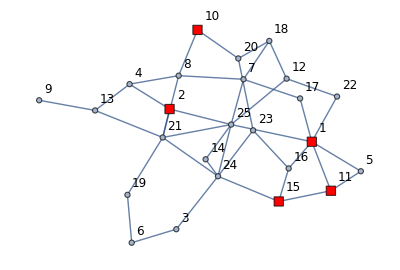

```mathematica
{graph15, weightAssociation15, terminals15} = generateSteinerProblemInstanceRG[25, 40, 5, WeightBounds ->{1, 1000}];
drawGraph[graph15, terminals15, VertexLabelStyle->Directive[Black,12],ImageSize->400]
```

```mathematica
DumpSave["dump/nice_small.mx", {graph15, weightAssociation15, terminals15}];
```

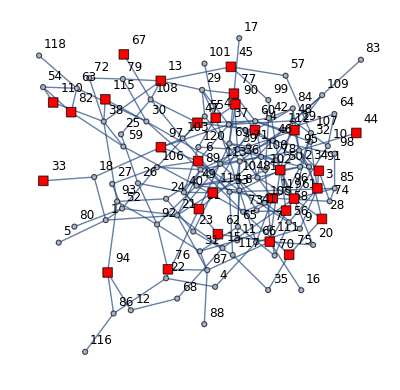

```mathematica
{graph100, weightAssociation100, terminals100} = generateSteinerProblemInstanceRG[120, 220, 30, WeightBounds ->{1, 1000}];
drawGraph[graph100, terminals100, VertexLabelStyle->Directive[Black,12], TerminalSize->1.25, ImageSize->400]
```

```mathematica
DumpSave["dump/nice_medium.mx", {graph100, weightAssociation100, terminals100}];
```

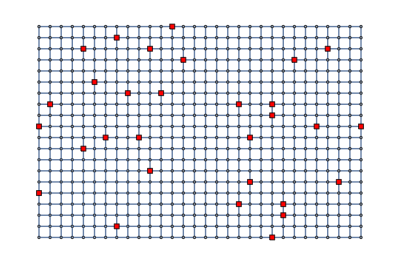

```mathematica
{graphGrid, terminalsGrid} = generateSteinerProblemInstanceGrid[20, 30, 30];
drawGraph[graphGrid, terminalsGrid, VertexLabelStyle->Directive[Black,12],ImageSize->400, VertexLabels->None]
```

```mathematica
DumpSave["dump/nice_grid_new.mx", {graphGrid, terminalsGrid}];
```

### SteinLib

```mathematica
getInstancesList["steinlib\\D"];
```

```mathematica
{stlibTestGraph, stlibTestWeights, stlibTestTerminals} = importSteinLibInstance["steinlib\\D\\d20.stp"];
```

```mathematica
VertexCount[stlibTestGraph]
EdgeCount[stlibTestGraph]
Length@stlibTestTerminals
```

1000

25000

500

```mathematica
getInstancesList["steinlib\\PUC"];
```

```mathematica
{stlibTestGraph, stlibTestWeights, stlibTestTerminals} = importSteinLibInstance["steinlib\\PUC\\bip52p.stp"];
```

```mathematica
VertexCount[stlibTestGraph]
EdgeCount[stlibTestGraph]
Length@stlibTestTerminals
```

2200

7997

200

```mathematica
DumpSave["dump/bip52p.mx", {stlibTestGraph, stlibTestTerminals}];
```

```mathematica
getInstancesList["steinlib\\SP"]
```

{steinlib\SP\antiwheel5.stp,steinlib\SP\design432.stp,steinlib\SP\oddcycle3.stp,steinlib\SP\oddwheel3.stp,steinlib\SP\se03.stp,steinlib\SP\w13c29.stp,steinlib\SP\w23c23.stp,steinlib\SP\w3c571.stp}

```mathematica
{stlibTestGraph, stlibTestWeights, stlibTestTerminals} = importSteinLibInstance["steinlib\\SP\\se03.stp"];
```

```mathematica
VertexCount[stlibTestGraph]
EdgeCount[stlibTestGraph]
Length@stlibTestTerminals
```

13

21

4

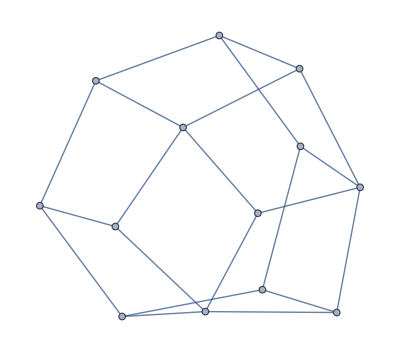
{-Graphics-,{1,8,10,12}}

```mathematica
DumpSave["dump/sp.mx", {stlibTestGraph, stlibTestTerminals}]
```

## Visualization

### Examples

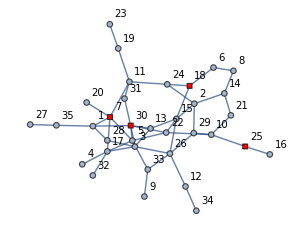

```mathematica
drawGraph[graph15,
terminals15,
VertexLabelStyle->Directive[Black,10],
VertexSize->0.85]
```

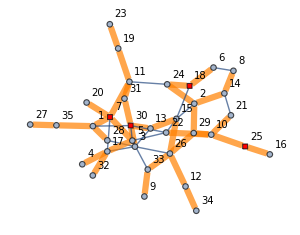

```mathematica
drawGraphSubgraph[graph15,
EdgeList@FindSpanningTree[graph15],
terminals15,
VertexLabelStyle->Directive[Black,10],
VertexSize->0.85]
```

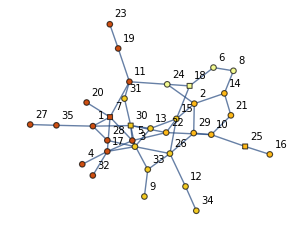

```mathematica
drawGraph[graph15,terminals15, VertexLabelStyle->Directive[Black,10],
VertexStyleFunc->voronoiVertexStyle[VertexList@graph15, Normal[dijkstraVoronoi[graph15, terminals15]["voronoi"]]],
VertexSize->0.85]
```

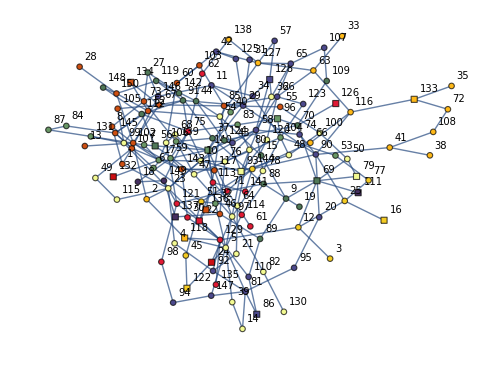

```mathematica
drawGraph[graph100, terminals100, VertexLabelStyle->Directive[Black,10],
VertexStyleFunc->voronoiVertexStyle[VertexList@graph100, Normal[dijkstraVoronoi[graph100, terminals100]["voronoi"]]],
TerminalSize->1.25, ImageSize->500]
```

### Animation export

```mathematica
dijkstraVoronoi[graph15, terminals15];
voronoiVertexStyle[VertexList@graph15, Normal[%["voronoi"]]]⟦%["order"]⟧;
a = Table[
drawGraph[graph15,terminals15, VertexLabelStyle->Directive[Black,10],
 VertexStyleFunc->%⟦;;step⟧,
TerminalSize->0.65,
ImageSize->500]
,
{step, 1,VertexCount@graph15, 1}];
```

```mathematica
Export["visual/steiner_voronoi.gif", a, "GIF" , "ControlAppearance"->None,"DisplayDurations"->0.5,ImageSize->700];
```

## Exact algorithms

### Dynamic programming (Dreyfus – Wagner) [1][3][4][5]

#### Description

```mathematica
-Graphics-
-Graphics-
```

Asymptotic time is : O (3^t n+2^t n^2+poly()), where t = #Terminals. n = #Vertices.

#### Examples

{0.206017,Null}

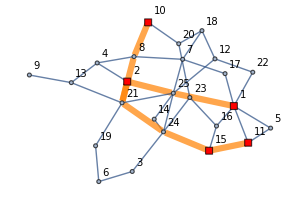
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 1605.

```mathematica
({resultDreyfusWagner15, treeDreyfusWagner15} = runDreyfusWagner[graph15, terminals15]);//AbsoluteTiming
gridResult[graph15,  terminals15, treeDreyfusWagner15, resultDreyfusWagner15]
```

{266.469,Null}

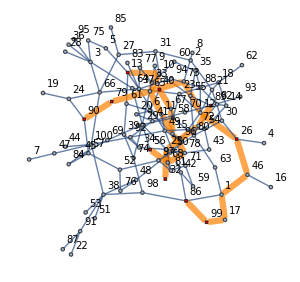
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 7175.

```mathematica
({resultDreyfusWagner100, treeDreyfusWagner100} = runDreyfusWagner[graph100, terminals100]);//AbsoluteTiming
gridResult[graph100,  terminals100, treeDreyfusWagner100, resultDreyfusWagner100]
```

{0.0356059,Null}

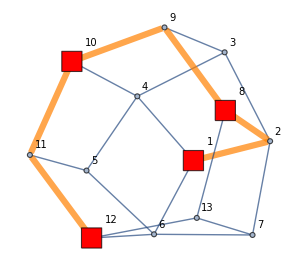
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 12.

```mathematica
({resultDreyfusWagnerStlibTest, treeDreyfusWagnerStlibTest} = runDreyfusWagner[stlibTestGraph, stlibTestTerminals]);//AbsoluteTiming
gridResult[stlibTestGraph, stlibTestTerminals, treeDreyfusWagnerStlibTest, resultDreyfusWagnerStlibTest]
```

{115.794,Null}

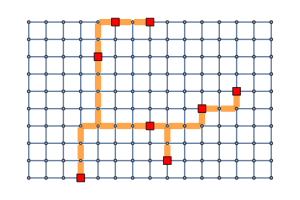
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 25.

```mathematica
({resultDreyfusWagnerGrid, treeDreyfusWagnerGrid} = runDreyfusWagner[graphGrid, terminalsGrid]);//AbsoluteTiming
gridResult[graphGrid, terminalsGrid, treeDreyfusWagnerGrid, resultDreyfusWagnerGrid, VertexLabels->None]
```

## Voronoi

### Examples

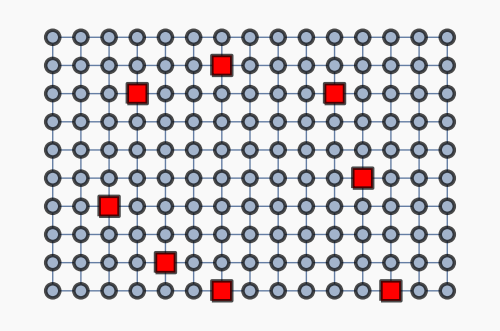

```mathematica
drawGraph[graphGrid, terminalsGrid,
 VertexLabelStyle->Directive[Black,10], ImageSize->500, VertexLabels->None,
VertexSize->Join[(# -> 0.5&/@ Complement[VertexList@graphGrid, terminalsGrid]), (# -> 0.8& /@terminalsGrid)],
Background->GrayLevel[0.975], BaseStyle->{Thick, EdgeForm[Thickness[0.005]]}]
```

```mathematica
ColorData/@ColorData["Indexed"]
```

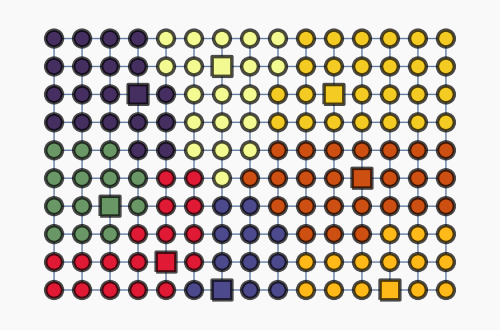

```mathematica
drawGraph[graphGrid, terminalsGrid, VertexLabelStyle->Directive[Black,10],
VertexStyleFunc->voronoiVertexStyle[VertexList@graphGrid, Normal[dijkstraVoronoi[graphGrid, terminalsGrid]["voronoi"]]],
ImageSize->500, VertexLabels->None,
VertexSize->Join[(# -> 0.6& /@ Complement[VertexList@graphGrid, terminalsGrid]), (# -> 0.8& /@terminalsGrid)],
Background->GrayLevel[0.975], BaseStyle->{Thick, EdgeForm[Thickness[0.005]]}]
```

## Leftist Heap

### Examples

```mathematica
ClearAll[a,b,c]
```

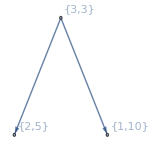
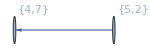

```mathematica
a = leftistHeapHeapify[{{1, 10}, {2, 5}, {3, 3}}];
b = leftistHeapHeapify[{{4, 7}, {5, 2}}];
Row[{leftistHeapDraw[a], leftistHeapDraw[b]}]
```

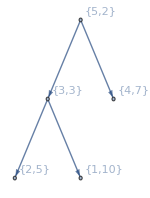

```mathematica
leftistHeapMeldClearly[c,a, b];
leftistHeapDraw[c]
```

5

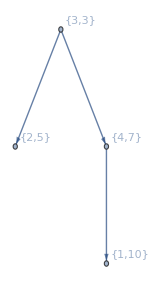

```mathematica
leftistExtractMin@c
leftistHeapDraw[c]
```

```mathematica
ClearAll[a,b,c]
```

## Approximation algorithms

### 2-approximation (Kou – Markowsky – Berman) [1][2]

#### Description

```mathematica
-Graphics-
-Graphics-
-Graphics-
```

### 2-approximation (Mehlhorn) [7][8]

#### Description

Mehlhorn's algorithm (improvement of previous algorithm):
1. Build Auxilary graph (AG):
	- build Voronoi diagram of graph.
	- create new graph AG.
	- for all border edges (u, v) add to AG edge (voronoi_center[u], voronoi_center[v]) with weight distance(voronoi_center[u], u) + distance(voronoi_center[v], v) + weight[(u, v)].
2. Find MinSpanningTree in AG.
3. Find original graph subgraph of short-paths accordind to auxilary spanning tree.
4. Find MinSpanningTree of that subgraph.
5. Cut it, to make Steiner-tree.

### Examples

#### 15

```mathematica
(treeKouMarkowskyBerman15 = runKouMarkowskyBerman[graph15, terminals15]);//AbsoluteTiming
resultKouMarkowskyBerman15 = edgeWeightSum[graph15, treeKouMarkowskyBerman15]
gridResult[graph15,  terminals15, treeKouMarkowskyBerman15, resultKouMarkowskyBerman15]
```

{0.054568,Null}

1605

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 1605

```mathematica
(treeMehlhorn15 = runMehlhorn[graph15, terminals15]);//AbsoluteTiming
resultMehlhorn15 = edgeWeightSum[graph15, treeMehlhorn15]
gridResult[graph15,  terminals15, treeMehlhorn15, resultMehlhorn15]
```

{0.90331,Null}

1605

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 1605

#### 100

{0.127007,Null}

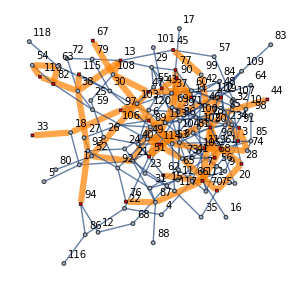
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 13947

```mathematica
(treeKouMarkowskyBerman100 = runKouMarkowskyBerman[graph100, terminals100]);//AbsoluteTiming
resultKouMarkowskyBerman100 = edgeWeightSum[graph100, treeKouMarkowskyBerman100];
gridResult[graph100,  terminals100, treeKouMarkowskyBerman100, resultKouMarkowskyBerman100]
```

```mathematica
(treeMehlhorn100 = runMehlhorn[graph100, terminals100]);//AbsoluteTiming
resultMehlhorn100 = edgeWeightSum[graph100, treeMehlhorn100];
gridResult[graph100,  terminals100, treeMehlhorn100, resultMehlhorn100]
```

{0.0184657,Null}

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 13947

#### Stlib

```mathematica
TimeConstrained[(treeKouMarkowskyBermanStlib = runKouMarkowskyBerman[stlibTestGraph, stlibTestTerminals]);//AbsoluteTiming,
300, "More than 300 sec."]
```

More than 300 sec.

```mathematica
(treeMehlhornStlibTest = runMehlhorn[stlibTestGraph, stlibTestTerminals]);//AbsoluteTiming
resultMehlhornStlibTest = edgeWeightSum[stlibTestGraph, treeMehlhornStlibTest]
steinerSolutionQ[treeMehlhornStlibTest, stlibTestTerminals]
gridResult[stlibTestGraph, stlibTestTerminals, treeMehlhornStlibTest, resultMehlhornStlibTest];
```

{0.537329,Null}

37452

True

#### GridGraph

{0.0694543,Null}

119

True

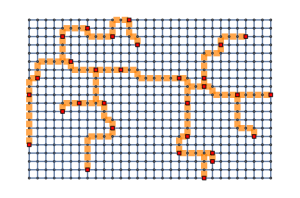
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 119

```mathematica
(treeMehlhornGridTest = runMehlhorn[graphGrid, terminalsGrid]);//AbsoluteTiming
resultMehlhornGridTest = edgeWeightSum[graphGrid, treeMehlhornGridTest]
steinerSolutionQ[treeMehlhornGridTest, terminalsGrid]
gridResult[graphGrid, terminalsGrid, treeMehlhornGridTest, resultMehlhornGridTest, VertexLabels->None]
```

## Greedy algorithms [6][7]

### Shortest-path heuristic (SPH)

#### Description

Algorithms starts from one-vertex tree containing only terminal t and consequently adds paths to closest (to tree vertices) terminal, that was not added yet.

### Repeated SPH (RSPH)

#### Description

In RSPH basic SPH is being used multiple times from different start terminals, and then best solution is chosen.
RSPH uses universal distance-matrix for all starts of SPH to avoid recomputations.

### Examples

```mathematica
(treeRSP15 = steinerRepeatedShortestPathHeuristic[graph15, terminals15, 100])//AbsoluteTiming
resultRSP15 = edgeWeightSum[graph15, treeRSP15]
steinerSolutionQ[treeRSP15, terminals15]
gridResult[graph15,  terminals15, treeRSP15, resultRSP15]
```

{0.0283555,{11<->15,15<->24,24<->21,21<->2,21<->8,2<->25,25<->1,8<->10}}

1605

True

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 1605

{0.779364,Null}

True

13515

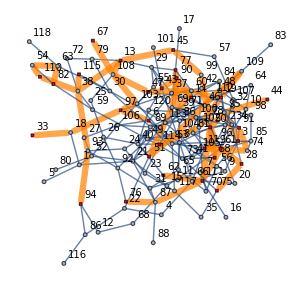
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 13515

```mathematica
(treeSP100 = steinerRepeatedShortestPathHeuristic[graph100, terminals100, 100]);//AbsoluteTiming
steinerSolutionQ[treeSP100, terminals100]
resultSP100 = edgeWeightSum[graph100, treeSP100]
gridResult[graph100,  terminals100, treeSP100, resultSP100]
```

{0.006499,Null}

True

12

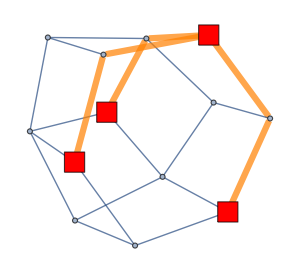
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 12

```mathematica
(treeSPStlib = steinerRepeatedShortestPathHeuristic[stlibTestGraph, stlibTestTerminals, 100]);//AbsoluteTiming
steinerSolutionQ[treeSPStlib, stlibTestTerminals]
resultSPStlib= edgeWeightSum[stlibTestGraph, treeSPStlib]
gridResult[stlibTestGraph,  stlibTestTerminals, treeSPStlib, resultSPStlib, VertexLabels->None]
```

{6.30919,Null}

True

112

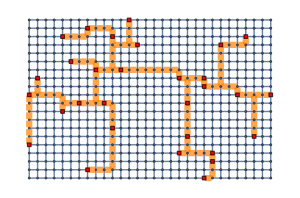
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 112

```mathematica
(treeSPGrid = steinerRepeatedShortestPathHeuristic[graphGrid, terminalsGrid, 100]);//AbsoluteTiming
steinerSolutionQ[treeSPGrid, terminalsGrid]
resultSPGrid = edgeWeightSum[graphGrid, treeSPGrid]
gridResult[graphGrid,  terminalsGrid, treeSPGrid, resultSPGrid, VertexLabels->None]
```

```mathematica
(* Big stlib instance *)
(treeSPStlib = steinerRepeatedShortestPathHeuristic[stlibTestGraph, stlibTestTerminals, 100]);//AbsoluteTiming
steinerSolutionQ[treeSPStlib, stlibTestTerminals]
resultSPStlib= edgeWeightSum[stlibTestGraph, treeSPStlib]
```

{101.29,Null}

True

28895

## Local-search algorithms [7]

### General Description

fact: Given weighted graph G, for any S - feasible solution of steiner tree problem, it is true that MST[V(S)] ≤ S (by total weight), where MST[S] -- minimal spanning tree of vertices X in G. 

def: Steiner-vertex is a vertex is S that is not terminal, i.e. S \ T.
def. Crucial-vertex is a vertex in S that is either terminal or has degree >= 3 in S.

There are 3 local-search algorithms below:
1) Steiner-vertex insertion. (VI)
2) Steiner-vertex elimination. (VE)
3) Key-path exchange. (PE)

First 2 algorithms are based on principle of editing V(T) (inserting or eliminating steiner-vertex), and recalculating MST, trying to get improvement of solution.

Key-path exchange algorithm for any path between 2 crusial vertices, that contain's no more crucial vertices, tries to elimnate it and then reconnect resulting graph components in shortest possible way (so, exchange paths).

Also there are 2 combinations of algorithms above presented:
1) VIVE
2) PEVIVE

### Steiner-Vertex Insertion

#### Examples

```mathematica
tree = steinerVertexInsertionFixedPoint[graph15, treeMehlhorn15]
steinerSolutionQ[tree, terminals15]
edgeWeightSum[graph15, tree]
edgeWeightSum[graph15, treeMehlhorn15]
```

{2<->25,2<->21,25<->1,11<->15,15<->24,21<->24,21<->8,8<->10}

True

1605

1605

```mathematica
tree = steinerVertexInsertionFixedPoint[graph100, treeMehlhorn100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[graph100, tree]
edgeWeightSum[graph100, treeMehlhorn100]
```

{33<->18,18<->97,97<->103,97<->6,19<->71,19<->102,71<->89,89<->21,21<->52,47<->106,47<->108,47<->60,106<->52,114<->102,13<->108,13<->38,108<->103,108<->67,60<->39,39<->77,50<->95,50<->96,50<->111,50<->99,50<->58,95<->3,95<->44,96<->119,119<->74,119<->53,111<->61,111<->62,111<->87,45<->99,61<->28,28<->75,74<->91,53<->103,51<->69,51<->104,69<->90,90<->43,90<->14,104<->49,49<->73,75<->73,87<->76,110<->38,110<->54,38<->93,38<->115,94<->93,54<->63,82<->63}

True

13947

13947

```mathematica
tree = steinerVertexInsertionFixedPoint[graphGrid, treeMehlhornGridTest];
steinerSolutionQ[tree, terminalsGrid]
edgeWeightSum[graphGrid, tree]
edgeWeightSum[graphGrid, treeMehlhornGridTest]
```

True

119

119

```mathematica
tree =  steinerVertexInsertionFixedPoint[graph100, treeSP100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[graph100, tree]
edgeWeightSum[graph100, treeSP100]
```

{79<->90,79<->65,65<->10,65<->11,65<->73,10<->13,89<->72,72<->25,25<->32,25<->68,11<->15,15<->67,15<->78,67<->40,73<->12,12<->26,26<->46,78<->68,68<->56,46<->1,1<->17,17<->99,99<->86}

True

7175

7175

```mathematica
tree = steinerVertexInsertionFixedPoint[stlibTestGraph, treeMehlhornStlibTest];
steinerSolutionQ[tree, stlibTestTerminals]
edgeWeightSum[stlibTestGraph, tree]
edgeWeightSum[stlibTestGraph, treeMehlhornStlibTest]
```

True

540

542

### Steiner-Vertex Elimination

#### Examples

```mathematica
tree = steinerVertexEliminationFixedPoint[graph15, treeMehlhorn15, terminals15]
steinerSolutionQ[tree, terminals15]
edgeWeightSum[graph15, tree]
edgeWeightSum[graph15, treeMehlhorn15]
```

{2<->25,2<->21,25<->1,11<->15,15<->24,21<->24,21<->8,8<->10}

True

1605

1605

```mathematica
tree = steinerVertexEliminationFixedPoint[graph100, treeMehlhorn100, terminals100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[graph100, tree]
edgeWeightSum[graph100, treeMehlhorn100]
```

{3<->95,6<->97,13<->38,13<->45,13<->108,14<->90,18<->33,18<->97,19<->71,21<->52,21<->89,21<->114,28<->61,28<->75,38<->93,38<->110,38<->115,39<->60,39<->77,43<->90,44<->95,45<->99,47<->60,47<->106,47<->108,49<->73,49<->104,50<->58,50<->95,50<->96,50<->99,50<->111,51<->69,51<->104,52<->106,54<->63,54<->110,61<->111,62<->111,63<->82,67<->108,69<->90,71<->89,73<->75,74<->91,74<->119,76<->87,87<->111,93<->94,96<->119,97<->103,103<->108}

True

13784

13947

```mathematica
tree = steinerVertexEliminationFixedPoint[graphGrid, treeMehlhornGridTest, terminalsGrid];
steinerSolutionQ[tree, terminalsGrid]
edgeWeightSum[graphGrid, tree]
edgeWeightSum[graphGrid, treeMehlhornGridTest]
```

True

119

119

```mathematica
tree =  steinerVertexEliminationFixedPoint[graph100, treeSP100, terminals100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[graph100, tree]
edgeWeightSum[graph100, treeSP100]
```

{77<->39,39<->60,60<->47,60<->112,47<->108,112<->109,112<->104,109<->19,19<->102,108<->13,108<->67,108<->103,13<->45,13<->38,103<->97,97<->6,97<->18,45<->99,99<->50,50<->95,50<->96,50<->58,50<->111,95<->3,95<->44,96<->119,119<->74,74<->91,111<->61,111<->62,111<->87,61<->28,87<->76,28<->75,104<->51,51<->69,38<->110,38<->115,38<->93,110<->54,69<->90,90<->14,90<->43,102<->114,54<->63,63<->82,18<->33,93<->94}

True

13515

13515

```mathematica
tree = steinerVertexEliminationFixedPoint[stlibTestGraph, treeMehlhornStlibTest, stlibTestTerminals];
steinerSolutionQ[tree, stlibTestTerminals]
edgeWeightSum[stlibTestGraph, tree]
edgeWeightSum[stlibTestGraph, treeMehlhornStlibTest]
```

True

27090

37452

### VIVE

#### Examples

```mathematica
tree = steinerVIVEFixedPoint[graph15, treeMehlhorn15, terminals15]
steinerSolutionQ[tree, terminals15]
edgeWeightSum[graph15, tree]
edgeWeightSum[graph15, treeMehlhorn15]
```

{2<->25,2<->21,25<->1,11<->15,15<->24,21<->24,21<->8,8<->10}

True

1605

1605

```mathematica
tree = steinerVIVEFixedPoint[graph100, treeMehlhorn100, terminals100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[graph100, tree]
edgeWeightSum[graph100, treeMehlhorn100]
```

{3<->95,6<->97,13<->38,13<->45,13<->108,14<->90,18<->33,18<->97,19<->71,21<->52,21<->89,21<->114,28<->61,28<->75,38<->93,38<->110,38<->115,39<->60,39<->77,43<->90,44<->95,45<->99,47<->60,47<->106,47<->108,49<->73,49<->104,50<->58,50<->95,50<->96,50<->99,50<->111,51<->69,51<->104,52<->106,54<->63,54<->110,61<->111,62<->111,63<->82,67<->108,69<->90,71<->89,73<->75,74<->91,74<->119,76<->87,87<->111,93<->94,96<->119,97<->103,103<->108}

True

13784

13947

```mathematica
tree = steinerVIVEFixedPoint[graphGrid, treeMehlhornGridTest, terminalsGrid];
steinerSolutionQ[tree, terminalsGrid]
edgeWeightSum[graphGrid, tree]
edgeWeightSum[graphGrid, treeMehlhornGridTest]
```

True

119

119

```mathematica
tree =  steinerVIVEFixedPoint[graph100, treeSP100, terminals100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[graph100, tree]
edgeWeightSum[graph100, treeSP100]
```

{1<->8,1<->23,5<->81,5<->93,5<->118,8<->102,10<->23,10<->93,16<->25,17<->102,17<->132,22<->113,24<->97,25<->90,26<->58,26<->85,26<->120,45<->51,45<->122,47<->56,47<->76,47<->97,47<->139,51<->144,58<->74,58<->128,67<->102,67<->134,69<->70,69<->79,69<->111,70<->96,70<->126,74<->90,75<->83,75<->113,75<->149,76<->80,80<->93,81<->86,83<->96,85<->117,90<->116,90<->144,93<->120,113<->140,116<->133,117<->136,137<->149,139<->140}

True

16725

18762

```mathematica
tree = steinerVIVEFixedPoint[stlibTestGraph, treeMehlhornStlibTest, stlibTestTerminals];
steinerSolutionQ[tree, stlibTestTerminals]
edgeWeightSum[stlibTestGraph, tree]
edgeWeightSum[stlibTestGraph, treeMehlhornStlibTest]
```

True

27090

37452

```mathematica
tree = steinerVIVEFixedPoint[graphGrid, treeMehlhornGridTest, terminalsGrid];
steinerSolutionQ[tree, terminalsGrid]
edgeWeightSum[graphGrid, tree]
edgeWeightSum[graphGrid, treeMehlhornGridTest]

gridResultCompare[graphGrid,  terminalsGrid, tree, treeMehlhornGridTest, edgeWeightSum[graphGrid, treeMehlhornGridTest]->edgeWeightSum[graphGrid, tree],
VertexLabels->None]
```

True

119

119

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 119→119

### Key-Path Exchange

#### Description [7]

Algorithm implementation is almost straight to one descripted in [7].

For reduction of shortest-path recalculations voronoi diagramms are used (dijkstraVoronoi), with centers in each vertex of original solution. Repairing of diagramm (in case of path elimination) are based on rerunning main step of dijkstraVoronoi, starting in border points of empty zones.

nb: Voronoi diagramm - partition of vertices of graph into sets, with respect to given set of centers C, such that vertex u is in one set with center c iff c is closest of centers to u (breaking of ties is irrelevant). Construction of diagramm implemented by running Dijkstra's algorithm simultaniously from all centers, additionally keeping an array of current centers for each vertex [7].

Key-path exchange algorithm main steps [7]: 
1. Build voronoi diagramm with centers in all nodes of base solution.
2. For each center priority queue (leftist heap) (meldable heap) is created. Then all edges, that are boundary (i.e. end points of edge have different centers in voronoi diagramm) are pushed to each of its centers heap with path cost as weight. 
3. Graph is being rooted, and is traversed from leaves to tops (dfs).
4. On accending of dfs key-paths are being found.
5. After sub-tree is traversed, all heaps in it's vertices are being meld in one.
6. Vertices are also carried in Disjoint Sets for easyness of checking which subtree they belong to.
7. After key-path is found, it is being tested on possibility of exchange. Algorithms finds best border-edge while repairing voronoi and testing saved boundary edges.

Also, implementation of algorithms allows multiple moves (exchanges) in one full iteration (by blocking possibilites for certain vertices to be in exchanging path, to avoid disconnection of graph).

```mathematica
-Graphics-
-Graphics-
```

#### Examples

```mathematica
tree =  steinerKeyPathExchangeFixedPoint[graph15, treeMehlhorn15, terminals15]
edgeWeightSum[graph15, tree]
edgeWeightSum[graph15, treeMehlhorn15]

gridResultCompare[graph15,  terminals15, tree, treeKouMarkowskyBerman15, edgeWeightSum[graph15, treeKouMarkowskyBerman15]->edgeWeightSum[graph15, tree]]
```

{2<->25,2<->21,25<->1,11<->15,15<->24,21<->24,21<->8,8<->10}

1605

1605

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 1605→1605

True

13794

13947

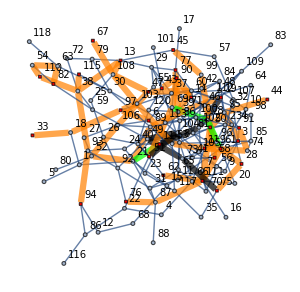
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 13947→13794

```mathematica
tree =  steinerKeyPathExchangeFixedPoint[graph100, treeMehlhorn100, terminals100];
steinerSolutionQ[tree, terminals100]
edgeWeightSum[graph100, tree]
edgeWeightSum[graph100, treeMehlhorn100]

gridResultCompare[graph100,  terminals100, tree, treeMehlhorn100, edgeWeightSum[graph100, treeMehlhorn100]->edgeWeightSum[graph100, tree]]
```

```mathematica
(tree =  steinerKeyPathExchangeFixedPoint[stlibTestGraph, treeMehlhornStlibTest, stlibTestTerminals]);//AbsoluteTiming
steinerSolutionQ[tree, stlibTestTerminals]
edgeWeightSum[stlibTestGraph, tree]
edgeWeightSum[stlibTestGraph, treeMehlhornStlibTest]
```

{52.2554,Null}

True

28746

37452

```mathematica
(tree =  steinerKeyPathExchangeFixedPoint[stlibTestGraph, treeSPStlib, stlibTestTerminals]);//AbsoluteTiming
steinerSolutionQ[tree, stlibTestTerminals]
edgeWeightSum[stlibTestGraph, tree]
edgeWeightSum[stlibTestGraph, treeSPStlib]
```

{16.4211,Null}

True

28042

28895

### PEVIVE

#### Examples

```mathematica
tree =  steinerPEVIVEFixedPoint[graph15, treeKouMarkowskyBerman15, terminals15]
steinerSolutionQ[tree, terminals15]
edgeWeightSum[graph15, tree]
edgeWeightSum[graph15, treeKouMarkowskyBerman15]
```

{10<->8,8<->21,21<->2,21<->24,2<->25,1<->25,15<->24,15<->11}

True

1605

1605

{3<->95,6<->97,13<->38,13<->45,13<->108,14<->90,18<->33,18<->97,19<->71,21<->52,21<->89,21<->114,28<->61,28<->75,38<->93,38<->110,38<->115,39<->60,39<->77,43<->90,44<->95,45<->99,47<->60,47<->106,47<->108,50<->58,50<->95,50<->96,50<->99,50<->111,51<->69,52<->106,54<->63,54<->110,61<->78,61<->111,62<->111,63<->82,67<->108,69<->78,69<->90,71<->89,74<->91,74<->119,76<->87,87<->111,93<->94,96<->119,97<->103,103<->108}

True

13773

13947

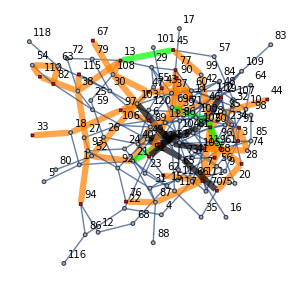
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 13947→13773

```mathematica
tree =  steinerPEVIVEFixedPoint[graph100, treeKouMarkowskyBerman100, terminals100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[graph100, tree]
edgeWeightSum[graph100, treeKouMarkowskyBerman100]

gridResultCompare[graph100,  terminals100, tree, treeKouMarkowskyBerman100, edgeWeightSum[graph100, treeKouMarkowskyBerman100]->edgeWeightSum[graph100, tree]]
```

```mathematica
tree =  steinerPEVIVEFixedPoint[graph100, treeSP100, terminals100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[graph100, tree]
edgeWeightSum[graph100, treeSP100]

gridResultCompare[graph100,  terminals100, tree, treeSP100,
edgeWeightSum[graph100, treeSP100]->edgeWeightSum[graph100, tree]]
```

{77<->39,39<->60,60<->47,60<->112,47<->108,112<->109,112<->104,109<->19,19<->102,108<->13,108<->67,108<->103,13<->45,13<->38,103<->97,97<->6,97<->18,45<->99,99<->50,50<->95,50<->96,50<->58,50<->111,95<->3,95<->44,96<->119,119<->74,74<->91,111<->61,111<->62,111<->87,61<->28,87<->76,28<->75,104<->51,51<->69,38<->110,38<->115,38<->93,110<->54,69<->90,90<->14,90<->43,102<->114,54<->63,63<->82,18<->33,93<->94}

True

13515

13515

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 13515→13515

```mathematica
(tree =  steinerPEVIVEFixedPoint[stlibTestGraph, treeMehlhornStlibTest, stlibTestTerminals]);//AbsoluteTiming
steinerSolutionQ[tree, stlibTestTerminals]
edgeWeightSum[stlibTestGraph, tree]
edgeWeightSum[stlibTestGraph, treeMehlhornStlibTest]
```

{112.028,Null}

True

511

729

{4.26307,Null}

114

119

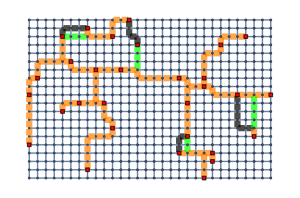
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 119→114

```mathematica
(tree = steinerPEVIVEFixedPoint[graphGrid, treeMehlhornGridTest, terminalsGrid]);//AbsoluteTiming
edgeWeightSum[graphGrid, tree]
edgeWeightSum[graphGrid, treeMehlhornGridTest]

gridResultCompare[graphGrid,  terminalsGrid, tree, treeMehlhornGridTest,
edgeWeightSum[graphGrid, treeMehlhornGridTest]->edgeWeightSum[graphGrid, tree],
VertexLabels->None]
```

111

112

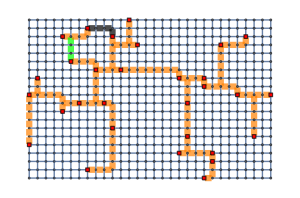
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 112→111

```mathematica
tree = steinerPEVIVEFixedPoint[graphGrid, treeSPGrid, terminalsGrid];
edgeWeightSum[graphGrid, tree]
edgeWeightSum[graphGrid, treeSPGrid]

gridResultCompare[graphGrid,  terminalsGrid, tree, treeSPGrid, edgeWeightSum[graphGrid, treeSPGrid]->edgeWeightSum[graphGrid, tree],
VertexLabels->None]
```

### Grid graph Examples

```mathematica
tree = steinerVertexInsertionFixedPoint[graphGrid, treeSPGrid];
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeSPGrid]
```

112

112

```mathematica
tree = steinerVertexInsertionFixedPoint[graphGrid, treeMehlhornGridTest];
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeMehlhornGridTest]
```

119

119

103

105

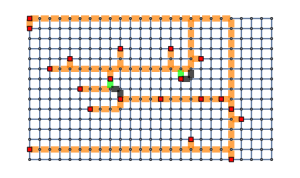
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 105→103

```mathematica
tree = steinerVertexEliminationFixedPoint[graphGrid, treeSPGrid, terminalsGrid];
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeSPGrid]

gridResultCompare[graphGrid,  terminalsGrid, tree, treeSPGrid, edgeWeightSum[graphGrid, treeSPGrid]->edgeWeightSum[graphGrid, tree],
VertexLabels->None]
```

67

70

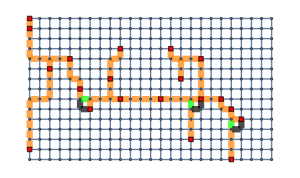
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 70→67

```mathematica
tree = steinerVertexEliminationFixedPoint[graphGrid, treeMehlhornGridTest, terminalsGrid];
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeMehlhornGridTest]

gridResultCompare[graphGrid,  terminalsGrid, tree, treeMehlhornGridTest, edgeWeightSum[graphGrid, treeMehlhornGridTest]->edgeWeightSum[graphGrid, tree],
VertexLabels->None]
```

False

25+76 $Failed

29+76 $Failed

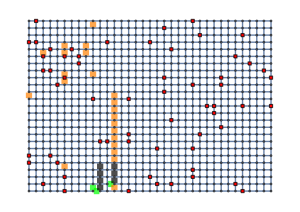
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 29+76 $Failed→25+76 $Failed

```mathematica
tree = steinerKeyPathExchangeFixedPoint[graphGrid, treeSPGrid, terminalsGrid];
steinerSolutionQ[tree, terminalsGrid]
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeSPGrid]

gridResultCompare[graphGrid,  terminalsGrid, tree, treeSPGrid, edgeWeightSum[graphGrid, treeSPGrid]->edgeWeightSum[graphGrid, tree],
VertexLabels->None]
```

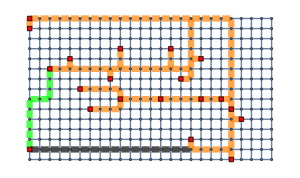
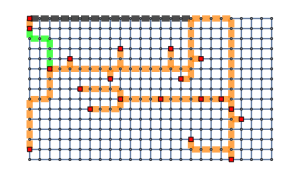
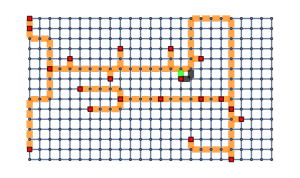
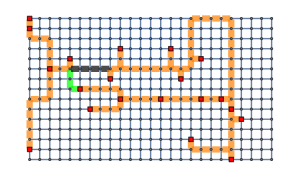
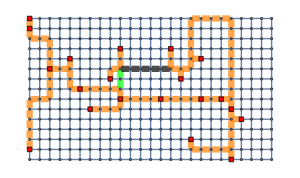
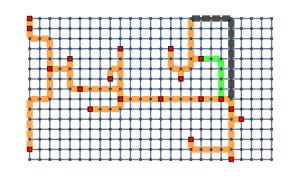
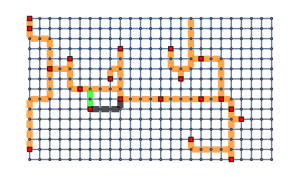

```mathematica
drawGraphSubgraphDifference[graphGrid, #⟦2⟧, #⟦1⟧, terminalsGrid, VertexLabels->None]&/@(Reap[steinerKeyPathExchange[graphGrid, treeSPGrid, terminalsGrid], "SolutionChange"]⟦2,1⟧)
```

```mathematica
gridMelhornFrames = (drawGraphSubgraphDifference[graphGrid, #⟦2⟧, #⟦1⟧, terminalsGrid, VertexLabels->None]&/@
Join[{{EdgeList@treeMehlhornGridTest, EdgeList@treeMehlhornGridTest}}, Reap[steinerKeyPathExchangeFixedPoint[graphGrid, treeMehlhornGridTest, terminalsGrid], "SolutionChange"]⟦2, 1⟧]);
```

```mathematica
Export["visual/key_path_exchange_grid_mehlhorn.gif", gridMelhornFrames, "GIF" , "ControlAppearance"->None,"DisplayDurations"->1,ImageSize->700];
```

{2.41637,Null}

True

165

174

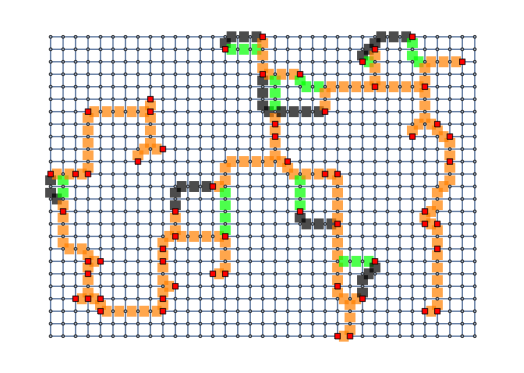
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 174→165

```mathematica
(tree = steinerKeyPathExchangeFixedPoint[graphGrid, treeMehlhornGridTest, terminalsGrid]);//AbsoluteTiming
steinerSolutionQ[tree, terminalsGrid]
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeMehlhornGridTest]

gridResultCompare[graphGrid,  terminalsGrid, tree, treeMehlhornGridTest, edgeWeightSum[graphGrid, treeMehlhornGridTest]->edgeWeightSum[graphGrid, tree],
VertexLabels->None]
```

True

69

105

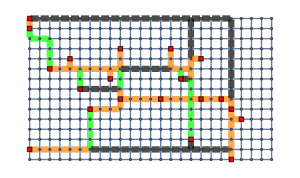
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 105→69

```mathematica
tree = steinerPEVIVEFixedPoint[graphGrid, treeSPGrid, terminalsGrid];
steinerSolutionQ[tree, terminalsGrid]
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeSPGrid]

gridResultCompare[graphGrid,  terminalsGrid, tree, treeSPGrid, edgeWeightSum[graphGrid, treeSPGrid]->edgeWeightSum[graphGrid, tree],
VertexLabels->None]
```

```mathematica
gridPEVIVEMelhornFramesReap = Join[{{EdgeList@treeMehlhornGridTest, EdgeList@treeMehlhornGridTest, "START"}}, Reap[steinerPEVIVEFixedPoint[graphGrid, treeMehlhornGridTest, terminalsGrid], "SolutionChange"]⟦2, 1⟧];

gridPEVIVEMelhornFrames = Grid[{{drawGraphSubgraphDifference[graphGrid, #⟦2⟧, #⟦1⟧, terminalsGrid, VertexLabels->None]}, {#⟦3⟧}}]&/@gridPEVIVEMelhornFramesReap;
```

```mathematica
Export["visual/pevive_grid_mehlhorn.gif", gridPEVIVEMelhornFrames, "GIF" , "ControlAppearance"->None,"DisplayDurations"->1,ImageSize->700];
```

{3.18337,Null}

True

65

70

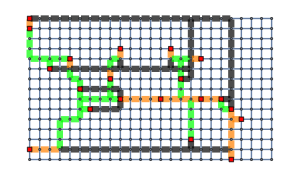
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 70→65

```mathematica
(tree = steinerPEVIVEFixedPoint[graphGrid, treeMehlhornGridTest, terminalsGrid];)//AbsoluteTiming
steinerSolutionQ[tree, terminalsGrid]
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeMehlhornGridTest]

gridResultCompare[graphGrid,  terminalsGrid, tree, treeSPGrid, edgeWeightSum[graphGrid, treeMehlhornGridTest]->edgeWeightSum[graphGrid, tree],
VertexLabels->None]
```

## Computations

### Random

```mathematica
test1=testerRandom[First[runDreyfusWagner[##]]&, {{PLCHDR, PLCHDR}}, Extract[generateSteinerProblemInstanceRG[##], {{1}, {3}}]&,
Table[{10, 15, t, WeightBounds ->{1, 100000}}, {t, 3, 7, 1}], 10, False]
```

{{{{PLCHDR,PLCHDR},{10,15,3,WeightBounds→{1,100000}}},0.00629692},{{{PLCHDR,PLCHDR},{10,15,4,WeightBounds→{1,100000}}},0.0174438},{{{PLCHDR,PLCHDR},{10,15,5,WeightBounds→{1,100000}}},0.0444081},{{{PLCHDR,PLCHDR},{10,15,6,WeightBounds→{1,100000}}},0.102412},{{{PLCHDR,PLCHDR},{10,15,7,WeightBounds→{1,100000}}},0.249451}}

```mathematica
test2=testerRandom[First[runDreyfusWagner[##]]&, {{PLCHDR, PLCHDR}}, Extract[generateSteinerProblemInstanceRG[##], {{1}, {3}}]&,
Table[{100, 150, t, WeightBounds ->{1, 100000}}, {t, 3, 8, 1}], 5, False]
```

{{{{PLCHDR,PLCHDR},{100,150,3,WeightBounds→{1,100000}}},0.556973},{{{PLCHDR,PLCHDR},{100,150,4,WeightBounds→{1,100000}}},1.41357},{{{PLCHDR,PLCHDR},{100,150,5,WeightBounds→{1,100000}}},2.89826},{{{PLCHDR,PLCHDR},{100,150,6,WeightBounds→{1,100000}}},7.063},{{{PLCHDR,PLCHDR},{100,150,7,WeightBounds→{1,100000}}},15.2095},{{{PLCHDR,PLCHDR},{100,150,8,WeightBounds→{1,100000}}},33.4486}}

{{3,0.556973},{4,1.41357},{5,2.89826},{6,7.063},{7,15.2095},{8,33.4486}}

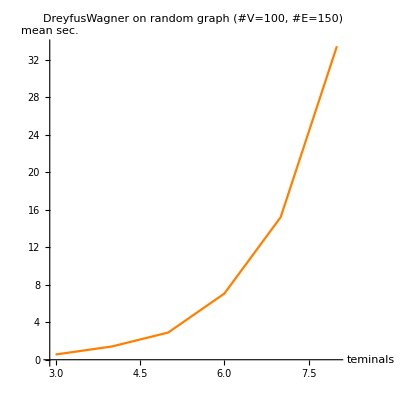

```mathematica
Transpose@{#⟦All, 1, 2, 3⟧, #⟦All, -1⟧}&@test2
ListLinePlot[%, PlotLabel->"DreyfusWagner on random graph (#V=100, #E=150)",
PlotStyle->Orange, AxesLabel->{"teminals", "mean sec."},
AspectRatio->1]
```

```mathematica
DumpSave["dump/test_data.mx", {test1, test2}];
```

```mathematica
testFunctionRandom[First[runDreyfusWagner[##]]&, {PLCHDR, PLCHDR}, Extract[generateSteinerProblemInstance[##], {{1}, {3}}]&, {15, 3, BernoulliProbability->0.125}, 100, False]
```

0.0128711

```mathematica
testFunctionRandom[First[runDreyfusWagner[##]]&, {PLCHDR, PLCHDR}, Extract[generateSteinerProblemInstance[##], {{1}, {3}}]&, {100, 7, BernoulliProbability->0.1}, 1, False]
```

14.2756

```mathematica
testerRandom[First[runDreyfusWagner[##]]&, {{PLCHDR, PLCHDR}}, Extract[generateSteinerProblemInstance[##], {{1}, {3}}]&, {{15, 3, BernoulliProbability->0.125}, {50, 5, BernoulliProbability->0.08}, {100, 7, BernoulliProbability->0.05}}, 1, False]
```

{{{{PLCHDR,PLCHDR},{15,3,BernoulliProbability→0.125}},0.011905},{{{PLCHDR,PLCHDR},{50,5,BernoulliProbability→0.08}},0.760988},{{{PLCHDR,PLCHDR},{100,10,BernoulliProbability→0.05}},183.929}}

### SteinLib import

```mathematica
getInstancesList["steinlib\\D"]
```

{steinlib\D\d01.stp,steinlib\D\d02.stp,steinlib\D\d03.stp,steinlib\D\d04.stp,steinlib\D\d05.stp,steinlib\D\d06.stp,steinlib\D\d07.stp,steinlib\D\d08.stp,steinlib\D\d09.stp,steinlib\D\d10.stp,steinlib\D\d11.stp,steinlib\D\d12.stp,steinlib\D\d13.stp,steinlib\D\d14.stp,steinlib\D\d15.stp,steinlib\D\d16.stp,steinlib\D\d17.stp,steinlib\D\d18.stp,steinlib\D\d19.stp,steinlib\D\d20.stp}

```mathematica
steinLibInstancesDList = (importSteinLibInstance[#]&/@getInstancesList["steinlib\\D"])⟦All, {1,3}⟧;
```

```mathematica
DumpSave["dump/steinlib_D.mx", {steinLibInstancesDList}];
```

```mathematica
<<"dump/steinlib_D.mx"
```

```mathematica
(*(steinLibInstancesDKou = tester[runKouMarkowskyBerman, steinLibInstancesDList, 10, First]);//AbsoluteTiming*)
```

```mathematica
(steinLibInstancesDMehlhorn = tester[runMehlhorn, steinLibInstancesDList, 1, First]);//AbsoluteTiming
```

{8.59042,Null}

```mathematica
DumpSave["dump/steinlib_D_sol.mx", {steinLibInstancesDMehlhorn}];
```

```mathematica
steinLibInfoD = Import["steinlib\\D_info.xlsx", "Data"]⟦1⟧;
steinLibInfoD = AssociationThread[Rest@First[steinLibInfoD], #]&/@Association[StringTrim[First[#]]->Rest[#]&/@Rest[steinLibInfoD]]
```

<|d01→<|vertices→1000 ,edges→1250 ,terminals→5 ,hardness→Ps ,opt→106 |>,d02→<|vertices→1000 ,edges→1250 ,terminals→10 ,hardness→Ps ,opt→220 |>,d03→<|vertices→1000 ,edges→1250 ,terminals→167 ,hardness→Ps ,opt→1565 |>,d04→<|vertices→1000 ,edges→1250 ,terminals→250 ,hardness→Ps ,opt→1935 |>,d05→<|vertices→1000 ,edges→1250 ,terminals→500 ,hardness→Ps ,opt→3250 |>,d06→<|vertices→1000 ,edges→2000 ,terminals→5 ,hardness→Ps ,opt→67 |>,d07→<|vertices→1000 ,edges→2000 ,terminals→10 ,hardness→Ps ,opt→103 |>,d08→<|vertices→1000 ,edges→2000 ,terminals→167 ,hardness→Ps ,opt→1072 |>,d09→<|vertices→1000 ,edges→2000 ,terminals→250 ,hardness→Ps ,opt→1448 |>,d10→<|vertices→1000 ,edges→2000 ,terminals→500 ,hardness→Ps ,opt→2110 |>,d11→<|vertices→1000 ,edges→5000 ,terminals→5 ,hardness→Pm ,opt→29 |>,d12→<|vertices→1000 ,edges→5000 ,terminals→10 ,hardness→Pm ,opt→42 |>,d13→<|vertices→1000 ,edges→5000 ,terminals→167 ,hardness→Ps ,opt→500 |>,d14→<|vertices→1000 ,edges→5000 ,terminals→250 ,hardness→Ps ,opt→667 |>,d15→<|vertices→1000 ,edges→5000 ,terminals→500 ,hardness→Ps ,opt→1116 |>,d16→<|vertices→1000 ,edges→25000 ,terminals→5 ,hardness→Pm ,opt→13 |>,d17→<|vertices→1000 ,edges→25000 ,terminals→10 ,hardness→Pm ,opt→23 |>,d18→<|vertices→1000 ,edges→25000 ,terminals→167 ,hardness→Ps ,opt→223 |>,d19→<|vertices→1000 ,edges→25000 ,terminals→250 ,hardness→Ps ,opt→310 |>,d20→<|vertices→1000 ,edges→25000 ,terminals→500 ,hardness→Ls ,opt→537.|>|>

```mathematica
#["opt"]&/@Values[steinLibInfoD]
```

{106 ,220 ,1565 ,1935 ,3250 ,67 ,103 ,1072 ,1448 ,2110 ,29 ,42 ,500 ,667 ,1116 ,13 ,23 ,223 ,310 ,537.}

```mathematica
steinLibInstancesDMehlhorn⟦All, 2, 1⟧
```

{0.0716533,0.0658933,0.0832569,0.0863118,0.113936,0.101591,0.0893658,0.119687,0.151846,0.163964,0.227789,0.217632,0.260439,0.327025,0.329513,1.16642,1.08197,1.22755,1.24915,1.32038}

```mathematica
steinLibDVert = ToExpression/@(#["opt"]&/@Values[steinLibInfoD])
steinLibDEdges = ToExpression/@(#["edges"]&/@Values[steinLibInfoD])
steinLibDTerm = ToExpression/@(#["terminals"]&/@Values[steinLibInfoD])
```

{106,220,1565,1935,3250,67,103,1072,1448,2110,29,42,500,667,1116,13,23,223,310,537.}

{1250,1250,1250,1250,1250,2000,2000,2000,2000,2000,5000,5000,5000,5000,5000,25000,25000,25000,25000,25000}

{5,10,167,250,500,5,10,167,250,500,5,10,167,250,500,5,10,167,250,500}

```mathematica
steinLibDOpt = ToExpression/@(#["opt"]&/@Values[steinLibInfoD])
```

{106,220,1565,1935,3250,67,103,1072,1448,2110,29,42,500,667,1116,13,23,223,310,537.}

```mathematica
steinLibDMehlhornTime  = steinLibInstancesDMehlhorn⟦All, 2, 1⟧
```

{0.0716533,0.0658933,0.0832569,0.0863118,0.113936,0.101591,0.0893658,0.119687,0.151846,0.163964,0.227789,0.217632,0.260439,0.327025,0.329513,1.16642,1.08197,1.22755,1.24915,1.32038}

```mathematica
steinLibDMehlhornSolValues = edgeWeightSum@@@Transpose[{steinLibInstancesDList⟦All, 1⟧,steinLibInstancesDMehlhorn⟦All, 2, 2⟧}]
```

{107,237,1608,1978,3263,73,105,1125,1513,2133,31,42,524,690,1137,15,25,248,335,542}

```mathematica
steinerSolutionQ@@@Transpose[{steinLibInstancesDMehlhorn⟦All, 2, 2⟧, steinLibInstancesDList⟦All, 2⟧}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
steinLibDMehlhornSolErr = N@Thread[Divide[(steinLibDMehlhornSolValues-steinLibDOpt), steinLibDOpt]]
```

{0.00943396,0.0772727,0.027476,0.0222222,0.004,0.0895522,0.0194175,0.0494403,0.0448895,0.0109005,0.0689655,0.,0.048,0.0344828,0.0188172,0.153846,0.0869565,0.112108,0.0806452,0.00931099}

```mathematica
Grid[Transpose[{{"Задача", "#Вершин", "#Ребер", "#Терминалов", "Оптимальное", "Мельхорн", "%Ошибки ^-3", "Время (сек.)"}}~Join~(Transpose[{Keys@steinLibInfoD, steinLibDVert, steinLibDEdges, steinLibDTerm, steinLibDOpt, steinLibDMehlhornSolValues,Round[steinLibDMehlhornSolErr, N@10^-3], Round[steinLibDMehlhornTime, N@10^-1]}]⟦{1, 5, 10, 15, 19, 20}⟧)~Join~{{"Среднее", "-", "-", "-", "-", "-", Round[Mean@steinLibDMehlhornSolErr, N@10^-3], Round[Mean@steinLibDMehlhornTime, N@10^-1]}}],
Frame->All]
```

Задача | d01 | d05 | d10 | d15 | d19 | d20 | Среднее
#Вершин | 106 | 3250 | 2110 | 1116 | 310 | 537. | -
#Ребер | 1250 | 1250 | 2000 | 5000 | 25000 | 25000 | -
#Терминалов | 5 | 500 | 500 | 500 | 250 | 500 | -
Оптимальное | 106 | 3250 | 2110 | 1116 | 310 | 537. | -
Мельхорн | 107 | 3263 | 2133 | 1137 | 335 | 542 | -
%Ошибки ^-3 | 0.009 | 0.004 | 0.011 | 0.019 | 0.081 | 0.009 | 0.048
Время (сек.) | 0.1 | 0.1 | 0.2 | 0.3 | 1.2 | 1.3 | 0.4

## References

[1] * Корте Б. Комбинаторная оптимизация. Теория и Алгоритмы / Бернард Корте, Йенс Фиген ; перевод с англ. М.А. Бабенко ; - М. : МЦНМО ; 2015 - 720 с.
[2] Markowski G. A fast algorithm for steiner trees / G. Markowski, L. Kou, L. Berman ; 1981.
[3] ^Fuchs B. Speeding up the Dreyfus-Wagner Algorithmfor minimum Steiner trees / B. Fuchs, W. Kern, X. Wang ; 2007
[4] *^ Fomin F.  Computing Optimal Steiner Trees in Polynomial Space / F. Fomin, F. Grandoni, D. Kratsch, D. Lokshtanov, S.Saurabh ; 2012
[5] Dreyfus S.  The Steiner Problem in Graphs / S. Dreyfus, R. Wagner ; 1971
[6] Plesnik J. Heuristics for the Steiner problem in graphs / J. Plesnik ; 1989
[7] *$ Uchoa E. Fast Local Search for Steiner Trees in Graphs / E. Uchoa, R. Werneck  ; 2010
[8] Mehlhorn K. A Faster Approximation Algorithm for the Steiner Tree Problem in Graphs / K. Mehlhorn ; 1988

^ - more theoretical
$ - more practical
* - nice paper